## What was the key graphical observation from Technology Assignment 2?
Key Graphical Observation: In most cases, if two regions are adjacent over a componant of the level set of f(x,y) corresponding to the level k, then on one side we get values smaller than k and on the other, values larger than k. 

In most cases, if the extreme value for a function “f” on a constraint curve “C” is the output “k”, then the level set of f corresponding to k is tangent to C.

## Some of these exercises come out of Rogowski’s text. In each, you are given a function f and a constraint curve C. For each:

1. Write a system of equations involving Lagrange multipliers whose solutions include the critical points.
2. Use NSolve (DO NOT FORGET THE DOUBLE EQUAL SIGNS ==) to solve that system of equations.
3. Find the max and min for f given the constraint C. (Don’t just give me the NSolve output. Tell me the point that gives the max and what the max is. Same for the min.)  Remember, for this to use Alt+7 when you type text. 

A. f(x,y)=5x-2y;              	C: x^2+y^2=9
B. f(x,y)=x^4 y^2                   	C: x^2+2 y^2=6
C. f(x,y)=(10x+100)/y        	C:x^2+(y-8)^2=1
D. f(x, y) = 4 x^2 - 9 y^2  	C: (x+2)^2-2y=11
E. f(x,y,z)=xy+4z                        C: x^2+2 y^2+3 z^2=6
F. f(x,y,z)=7x+3y-z             C: x+y=√(75+4(x-y)^2+z^2)




	 
For A : x^2+y^2=9
5=λ*2x
-2=λ*2y
Max is 16.155 at (2.78543,-1.11417)
Min is -16.1555 at (-2.78542,1.11417)

```mathematica
NSolve[x^2+y^2==9&&5==λ*2x&&-2==λ*2y&&5x-2y==k,{x,y,λ,k}, Reals]
```

{{x→2.78543,y→-1.11417,λ→0.897527,k→16.1555},{x→-2.78543,y→1.11417,λ→-0.897527,k→-16.1555}}

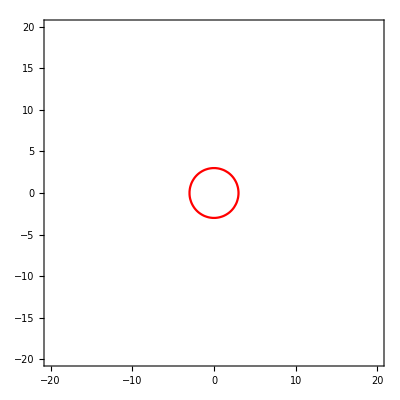

```mathematica
Show[ContourPlot[x^2+y^2==9,{x,-20,20},{y,-20,20},ContourStyle->Red]]
```

```mathematica
For B:
x^2+2y^2=6
4x^3*y^2=λ*2x
2x^4*y=λ*4y
Max is 16 at (-2,-1)
Min is 0 at (0,1.73205
```

```mathematica
NSolve[x^2+2*y^2==6&&4x^3*y^2==λ*2x&&2x^4*y==λ*4y&&x^4*y^2==k,{x,y,λ,k},Reals]
```

{{x→-2.,y→-1.,λ→8.,k→16.},{x→-2.,y→1.,λ→8.,k→16.},{x→2.,y→-1.,λ→8.,k→16.},{x→2.,y→1.,λ→8.,k→16.},{x→-2.44949,y→0.,λ→0.,k→0},{x→2.44949,y→0.,λ→0.,k→0},{x→0.,y→1.73205,λ→0.,k→0},{x→0.,y→1.73205,λ→0.,k→0},{x→0.,y→1.73205,λ→0.,k→0},{x→0.,y→-1.73205,λ→0.,k→0},{x→0.,y→-1.73205,λ→0.,k→0},{x→0.,y→-1.73205,λ→0.,k→0}}

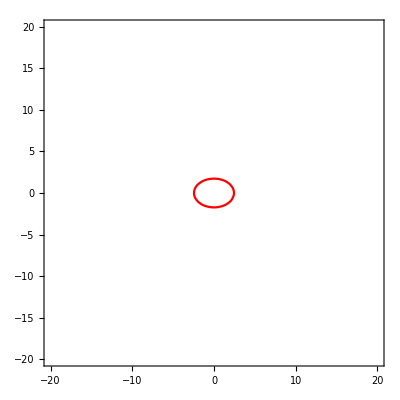

```mathematica
Show[ContourPlot[x^2+2y^2==6,{x,-20,20},{y,-20,20},ContourStyle->Red]]
```

```mathematica
For C:
x^2+(y-8)^2=1
10/y=λ*2x
(-10x-100)/y^2=λ*2(Y-8)
Max is 14.7249 at (0.5619,7.1727)
Min is 10.6719 at (-0.6837,8.7297)
```

```mathematica
NSolve[x^2+(y-8)^2==1&& 10/y ==λ*2x&& (-10x-100)/y^2==λ*2(y-8)&& (10x+100)/y==k,{x,y,λ,k},Reals]
```

{{x→-0.683763,y→8.7297,λ→-0.837654,k→10.6719},{x→0.561812,y→7.17274,λ→1.24078,k→14.7249}}

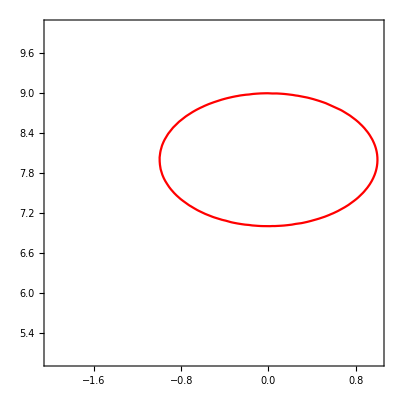

```mathematica
Show[ContourPlot[x^2+(y-8)^2==1,{x,-2,1},{y,5,10},ContourStyle->Red]]
```

```mathematica
For D:
(x+2)^2-2y=11
8x=λ*2(x+2)
-18y=-2λ
```

```mathematica
NSolve[(x+2)^2-2y==11&&8x==λ*2(x+2)&&-18y==-2λ&&4x^2-9y^2==k,{x,y,λ,k},Reals]
```

{{x→-1.85018,y→-5.48878,λ→-49.399,k→-257.447},{x→1.37068,y→0.180732,λ→1.62659,k→7.22105},{x→-5.52049,y→0.696934,λ→6.27241,k→117.532}}

```mathematica
Show[ContourPlot[(x+2)^2-2y==11,{x,-6,5},{y,-5,2},ContourStyle->Red]]
```

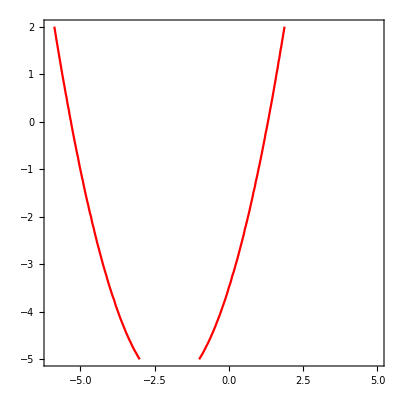

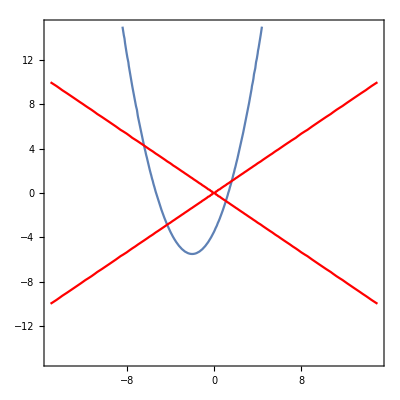

Set::write: Tag Times in 4 63.9931 is Protected.

```mathematica
Show[ContourPlot[(x+2)^2-2y==11,{x,-15,15},{y,-15,15}],ContourPlot[4x^2==9y^2,{x,-15,15},{y,-15,15},ContourStyle->Red]]
```

```mathematica
For E:
x^2+2y^2+3z^2=6
y=λ*2x
x=λ*4y
4=λ*6z
Max is 5.6568 at (0,0,1.4142)
Min is -5.6568 at (0,0,-1.4142)
```

```mathematica
NSolve[x^2+2y^2+3z^2==6&&y==λ*2x&&x==λ*4y&&4==λ*6z&&x*y+4z==k,{x,y,z,λ,k},Reals]
```

{{x→0.,y→0.,z→1.41421,λ→0.471405,k→5.65685},{x→0.,y→0.,z→-1.41421,λ→-0.471405,k→-5.65685}}

```mathematica
Show[ContourPlot3D[x^2+2y^2+3z^2==6,{x,-15,15},{y,-15,15},{z,-15,15}],ContourPlot3D[x*y==-4z,{x,-15,15},{y,-15,15},{z,-15,15},ContourStyle->Red]]
```

-Graphics3D-

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
For F:x+y==√(75+4(x-y)^2+z^2)
7=λ*(6x-10y)
3=λ*(-10x+6y)
-1=λ*2z
```

```mathematica
NSolve[x+y==√(75+4(x-y)^2+z^2)&&7==λ*(6x-10y)&&3==λ*(-10x+6y)&&-1==λ*2z&& 7x+3y-z==k,{x,y,z,λ,k},Reals]
```

{{x→4.06302,y→4.96592,z→1.80579,λ→-0.276887,k→41.5331}}

```mathematica
Show[ContourPlot3D[x+y==√(75+4(x-y)^2+z^2),{x,-15,15},{y,-15,15},{z,-15,15}],ContourPlot3D[7x+3y==z,{x,-15,15},{y,-15,15},{z,-15,15},ContourStyle->Red]]
```

-Graphics3D-

## Which point on the ellipse 4 x^2+25 y^2=49 is closest to the point (2,1)? Which is furthest? Explain.

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with (171802\ s)/178835 == 1. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/NSolve",
ButtonNote->"NSolve::infsolns"]

```mathematica
NSolve[x^2/(0.5)^2+y^2/(0.2)^2-7^2==0&&2(x-2)-(2*λ*x)/0.5^2==0&&2(y-1)-(2*λ*y)/0.5^2==0,{x,y,λ},Reals]
```

{{x→-2.18643,y→-1.09322,λ→0.478683},{x→2.18643,y→1.09322,λ→0.021317}}

For this problem I used the distance formula between a point (x,y) on the ellipse and the point (2,1)and put the equation of the ellipse into standard form. Then i used the Lagrange multiplier method  and set the distance equation equal to the equation of the ellipse multiplied by multiplier λ. Then i brought the λ*ellipse over the equal sign  and differentiated with respect to x and then y. I then used NSolve to solve a stem of equations that consisted of both partial derivatives and the equation of the ellipse in standard form.Based on visiual inspection,the point (-2.18643,-1.09322) is furthest from the point (2,1) and the point (2.18643,1.09322)is closest to the point (2,1).

## The corner of a building makes a 60^o angle.An architect wants to put fence outside the building around this corner to make a playground.The corner of the building will come into the playground (as in the picture below).He has 135 feet of fencing with which to work.What dimensions will maximize the area of the playground?How far from the corner of the bulding will he need to anchor the fence?

```mathematica
NSolve[x+2y==135&&1==λ*x&&2==λ(y-√3 x),{x,y,λ},Reals]
```

{{x→15.9497,y→59.5251,λ→0.062697}}

The maximum area of the playground is 729.097ft^2 with x and y demensions (15.95,59.52). The fence will be anchored 15.94 ft from the outward edge of the building along the hypotnuse of the triangle formed by the building and the inside of the playground cut horizontaly at the verticle edge of the building.

Bonus: 

1. Referring to part B, let P be the point on the ellipse which is closest to the point (2,1) and let Q be the furthest. Show that the vector from (2,1) to P and the vector from (2,1) to Q are both normal to the ellipse. Show that these are the only two points on the ellipse that have this property. In your own words, describe what you think is going on here.   

2. What are the level sets and what is the constraint surface in the last problem in Part A? Get a good picture describing what is going on.